```mathematica
$HistoryLength=0;

IntiateAgesMatrix[landmat_]:=Module[{mat},
mat=landmat/. 1:>RandomInteger[{1,125}];(*Initiates age at 1-125 at each habitable cell*)
mat]

CreateRandomLandscape[n_,Phabitat_]:=Module[{a1,m1,m2,m3},
a1=Sort[RandomSample[Flatten[Table[{i,j},{i,n},{j,n}],1],Round[Phabitat n^2]]];
m1=SparseArray[a1->Table[1,{Length[a1]}]];
m2=Normal[m1];
m2
]

Nextevent[ladscapematAges_,habitatpos_]:=Module[{ages,t1,t2,Minage},
ages=Table[ladscapematAges⟦k⟦1⟧,k⟦2⟧⟧,{k,habitatpos}];
Minage=Min[ages]; 
t1=Position[ladscapematAges,x_ /; x==Minage];
t2=Intersection[t1,habitatpos];
RandomChoice[t2]
]

(*Initial kernel - Uniform*)
InitiateDispK0[ladscapematPlain_,s_]:=Module[{w1},(*s is the number of bins in the dispersalK histogram. We now intiate everything with uniform kernals. Kernals must sum to 1*)
w1=ladscapematPlain/. 1->1/s Table[1,{s}];
w1
]

(*Initial kernel - 1 in bin 0, 0 otherwise (no dispersal)*)
InitiateDispK1[ladscapematPlain_,s_]:=Module[{w1},(*s is the number of bins in the dispersalK histogram. Kernals must sum to 1*)
w1=ladscapematPlain/. 1->Table[If[i==1,1,0],{i,s}];
w1
]

(*Initial kernel - 0.5 in bin 0 and s-1, 0 otherwise (bimodal dispersal)*)
InitiateDispK2[ladscapematPlain_,s_]:=Module[{w1},(*s is the number of bins in the dispersalK histogram. Kernals must sum to 1*)
w1=ladscapematPlain/. 1->Table[If[i==1||i==s,0.5,0],{i,s}];
w1
]

(*Initial kernel - 1 in last bin, 0 otherwise (long-distance dispersal)*)
InitiateDispK3[ladscapematPlain_,s_]:=Module[{w1},(*s is the number of bins in the dispersalK histogram. Kernals must sum to 1*)
w1=ladscapematPlain/. 1->Table[If[i==s,1,0],{i,s}];
w1
]

TorusEucludianDistance[a_,b_,n_]:=Module[{xdist,ydist},(**)
xdist=If[a⟦1⟧≤b⟦1⟧,
Min[{b⟦1⟧-a⟦1⟧,a⟦1⟧+n-b⟦1⟧}],
Min[{a⟦1⟧-b⟦1⟧,b⟦1⟧+n-a⟦1⟧}]
];
ydist=If[a⟦2⟧≤b⟦2⟧,
Min[{b⟦2⟧-a⟦2⟧,a⟦2⟧+n-b⟦2⟧}],
Min[{a⟦2⟧-b⟦2⟧,b⟦2⟧+n-a⟦2⟧}]
];
Sqrt[xdist^2+ydist^2]
]

CollectSeeds[Treeposition_,dispKmat_,habitatposList_,s_]:=Module[{potentialdoners},(*Selects a new tree position that will replace a dying tree (in Treeposition)*)
potentialdoners=Select[habitatposList,Floor[TorusEucludianDistance[Treeposition,#,Length[dispKmat]]]<=s-1&];
seedpile=Table[If[dispKmat⟦t⟦1⟧,t⟦2⟧⟧===0,0,If[Treeposition===t,1,1/(2 π TorusEucludianDistance[Treeposition,t,Length[dispKmat]])]*dispKmat[[t[[1]],t[[2]],Floor[TorusEucludianDistance[Treeposition,t,Length[dispKmat]]]+1]]],{t,potentialdoners}];
If[Total[seedpile]===0||Total[seedpile]===0.,seedpile=Table[1,Length[seedpile]]];
RandomChoice[seedpile->potentialdoners]
]

MutateDispK[dispK_,mu_,magnitude_]:=(*Here each bin in the dispersal kernel is tested if it mutates, then how much, and at the end the kernel s normalized*)Module[{t1},(*mu is the probability of a mutation occuring in one bin in one generation (more precisely, since it can be larger than one - the number of bins expected to change each generation); Magnitude is the maximal size of the mutation*)
t1=Table[If[RandomReal[]<mu/Length[dispK],Max[RandomReal[{v-magnitude,v+magnitude}],0],v],{v,dispK}];
If[Total[t1]===0||Total[t1]===0.,Table[1/Length[dispK],{Length[dispK]}],t1/Total[t1]](*Normalizes dispersal kernel to integrate to 1*)
]

DeathStep[Treeposition_,dispKmat_,habitatposList_,landdata_,s_,AgeMatrix_,mu_,magnitude_,time_]:=Module[{newtime,newseed,newAgeMatrix,newdispK,newdispKmat},(*Conduct the replacemnt of a =n individual by another individual*)
newtime=time+AgeMatrix[[Treeposition[[1]],Treeposition[[2]]]];
newseed=CollectSeeds[Treeposition,dispKmat,habitatposList,s];
newAgeMatrix=(AgeMatrix-AgeMatrix[[Treeposition[[1]],Treeposition[[2]]]])*landdata;
newAgeMatrix=ReplacePart[newAgeMatrix,Treeposition->RandomReal[NormalDistribution[100,5]]];
newdispK=MutateDispK[dispKmat[[newseed[[1]],newseed[[2]]]],mu,magnitude];
newdispKmat=ReplacePart[dispKmat,Treeposition->If[newseed===0,0,newdispK]];
{newAgeMatrix,newdispKmat,newtime}
]
landscapeShape[Hu_, size_] := (*Generate autocorrelated landscape*)
 Module[{r, a, phi, inq, rinq},
  q = ConstantArray[0, {size, size}];
  Do[
    Do[
     g = {If[i == 0, 0, size - i], If[j == 0, 0, size - j]};
     r = RandomReal[NormalDistribution[]];
     a = If[i == 0 && j == 0, 0, 
       r ((Min[{i, g[[1]]}])^2 + (Min[{j, g[[2]]}])^2)^((-Hu - 1)/
        2)]; 
     phi = RandomReal[{0, 2 π}];
     o1 = a Cos[phi] + I a Sin[phi];
     o2 = a Cos[phi] - I a Sin[phi];
     If[i == 0 && j == 0, o1 = Im[o1]];
     If[(i == 0 || i == size/2) && (j == 0 || j == size/2), 
      o1 = Re[o1]];
     If[q[[i + 1, j + 1]] == 0, 
      q = ReplacePart[q, {i + 1, j + 1} -> o1]; 
      q = ReplacePart[q, g + 1 -> o2]];
     , {j, 0, size - 1}]
    , {i, 0, size - 1}];
   inq = InverseFourier[q];
  rinq = Re[inq]
  ]

landscaperandom[size_]:=Module[{},(*Generate random landscape without autocorrelation*)
Table[Table[Random[],size],size]
]

landscapeChanging[landscapeShape_,time_,fragrate_,finalfrag_,size_]:=(*Fragmentation rate is measured in proportion of landscape lost per time-step; final frag is the final fragmentation rate, i.e. the p wherein fragmentation stops*)Module[{p,thr,m1},(*Creates landscape of size*size with Hurst index Hu and with p proportion of occupied cells*)
p=Max[{1-time*fragrate,finalfrag}];
If[0<p<1,
thr=Quantile[Flatten[landscapeShape],1-p];
m1=Map[If[#<=thr,0,1]&,landscapeShape,{2}]
];
If[p==0,m1=ConstantArray[0,{size,size}]];
If[p==1,m1=ConstantArray[1,{size,size}]];
m1
]

gridsatdist[r_]:=Module[{ta2,ta1}, (*number of cells in distance i from a focal cell (Subscript[g, i] in the*)
ta1=Flatten[Table[{i,j},{i,-r,r},{j,-r,r}],1];
ta2=Length[Select[ta1,Floor[EuclideanDistance[{0,0},#]]==r&]];
ta2
]

habitaatdist[Treeposition_,r_,habitatposList_,dispKmat_,Ngirdastdistlist_]:=Module[{ta1,ta2,ta0},
ta0=Length[Select[habitatposList,Floor[TorusEucludianDistance[Treeposition,#,Length[dispKmat]]]==r&]];
N[ta0/Ngirdastdistlist[[r+1]]]
]

lostseedspos[Treeposition_,habitatposList_,dispKmat_,s_,Ngirdastdistlist_]:=Module[{t1},
t1=Table[dispKmat⟦Treeposition⟦1⟧,Treeposition⟦2⟧,r+1⟧habitaatdist[Treeposition,r,habitatposList,dispKmat,Ngirdastdistlist],{r,0,s-1}];
1-Total[t1]
]
lostseeds[habitatposList_,dispKmat_,s_,Ngirdastdistlist_]:=Module[{},
Mean[Table[lostseedspos[i,habitatposList,dispKmat,s,Ngirdastdistlist],{i,habitatposList}]]
]



RunOneSim[initialkernel_,timelimit_,s_,mu_,mag_,Hu_,size_,fragrate_,finalfrag_]:=Module[{sims,meanDispKernelList,Ngirdastdistlist,time,landShape,landdata,agemat,habitatpos,DispKmat,flag1,flag2,step,mortalitylist,meanDispKmat,kernelat0,timelist1,timelist2,timelist3,ne,ds,OccupiedDispKernel,res},
sims={};
Ngirdastdistlist=Table[gridsatdist[r],{r,0,s-1}];
time=0;
landShape=If[Hu=="Random",landscaperandom[size],landscapeShape[Hu,size]];
landdata=landscapeChanging[landShape,0,fragrate,finalfrag,size];(*Intial landscape - uniform since time=0*)
agemat=IntiateAgesMatrix[landdata];
habitatpos=Sort[Position[landdata,1]];
DispKmat=Which[initialkernel==0,InitiateDispK0[landdata,s],initialkernel==1,InitiateDispK1[landdata,s],initialkernel==2,InitiateDispK2[landdata,s],initialkernel==3,InitiateDispK3[landdata,s]];(*Initial dispersal kernel; InitiateDispK0=Uniform; InitiateDispK1=no dispersal; InitiateDispK2=bimodal*)
flag1=0;
flag2=0;
step=1;
mortalitylist={lostseeds[habitatpos,DispKmat,s,Ngirdastdistlist]};
meanDispKmat=Mean[DeleteCases[Flatten[landdata*DispKmat,1],0]];
meanDispKernelList={meanDispKmat};
kernelat0={meanDispKmat[[1]]};
timelist1={0};
timelist2={0};
timelist3={0};
While[time<timelimit,
ne=Nextevent[agemat,habitatpos];
ds=DeathStep[ne,DispKmat,habitatpos,landdata,s,agemat,mu,mag,time];
agemat=ds[[1]];
DispKmat=ds[[2]];
time=ds[[3]];
If[time>=flag1,
OccupiedDispKernel=Select[Flatten[DispKmat,1],Total[#]==1.&];
meanDispKmat=Mean[OccupiedDispKernel];
AppendTo[meanDispKernelList,meanDispKmat];
AppendTo[kernelat0,meanDispKmat[[1]]];
AppendTo[timelist2,time];
 flag1=flag1+100;
];
If[time>=flag2,
AppendTo[mortalitylist,lostseeds[habitatpos,DispKmat,s,Ngirdastdistlist]];
AppendTo[timelist3,time];
flag2=flag2+1000
];
landdata=landscapeChanging[landShape,time,fragrate,finalfrag,size];
habitatpos=Sort[Position[landdata,1]];
agemat=agemat*landdata;
DispKmat=Table[landdata[[i,j]]*DispKmat[[i,j]],{i,Length[landdata]},{j,Length[landdata]}]
];
meanDispKmat=Mean[DeleteCases[Flatten[landdata*ds[[2]],1],0]];
res={meanDispKernelList,kernelat0,mortalitylist};
res
]
```

```mathematica
convergencetime=20000;(*How much time to allow for convergence after fragmentation process ends*)
NumberofBins=15; (*NUmber of dispersal classes in the dispersal kernel*)
NumberofMutatingBins=2;(*Mean number of bins mutating per reproduction event*)
MutationMagnitude=0.5; (*Mean magnitude of mutation per mutation*)
HurstIndex=0.2;(*a number or "Random"*)
LandSize=2^5; (*The landscape is a torus of size LandSize*LandSize *)
finalfrag=0.1; (*Final prportion of habitable cells at the end of the fragmentation process*)
fragrate=10^-3; (*The proportion of cells becoming inhabitable each time step (10^-3=rapid, 10^-4=intermediate, 10^-5=fast)*)
timelimit=Round[(1-finalfrag)/fragrate+convergencetime]; (*The overall simulation time, computed as the time of the fragmentation process + the time the simulation is run in the fragmented state*)
intialKernel=1;(*Intial Kernel - 0=Uniform; 1=NoDispersal; 2=BimodalDispersal; 3=LongDistance*)
```

```mathematica
(*This cell runs a single evolutionary trajectory based on the parameters in the green cell above*)
simres=RunOneSim[intialKernel,timelimit,NumberofBins,NumberofMutatingBins,MutationMagnitude,HurstIndex,LandSize,fragrate,finalfrag];
```

The output is a list of 3 objects:
(1) A list of length (timelimit/100 +2), where each element of the list is a list of length NumberofBins describing the mean dispersal kernel in the population at intervals of 100 time steps
(2) A list of length (timelimit/100 +2), where each element is the mean proportion of non-dispersers (d_0) in the population at intervals of 100 time steps
(3) A list of length (timelimit/1000 +2), where each element is the mean mortality rate (proportion of seeds dispersing to uninhabitable cells) in the population at intervals of 1000 time steps

### Final evolved dispersal kernel (from a single trajectory)

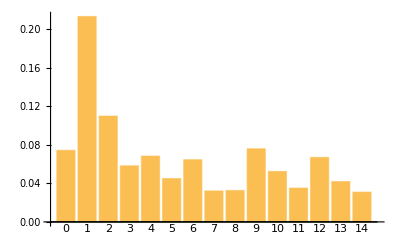

```mathematica
BarChart[Last[simres⟦1⟧],PlotRange->All,ChartLabels->Range[0,14]]
```

### Proportion of non-dispersers over time (a single evolutionary trajectory)

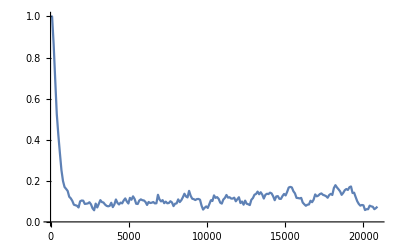

```mathematica
ListPlot[simres⟦2⟧,Joined->True,PlotRange->All,DataRange->{0,timelimit}]
```

### Dispersal-related seed mortality over time (a single evolutionary trajectory)

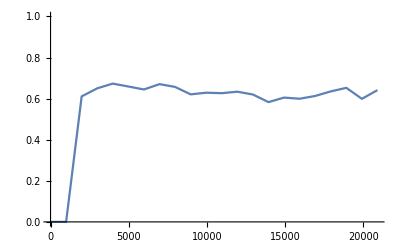

```mathematica
ListPlot[simres⟦3⟧,Joined->True,PlotRange->{0,1},DataRange->{0,timelimit}]
```